# non-destructive readout

P. Huft

Calculation for the non-destructive readout in the network experiment. 
Useful references:
- Kwon, et. al., “Parallel Low-Loss Measurement of Multiple Atomic Qubits” (the supplementary material is particularly helpful)

```mathematica
conj[z_]:=z/.{ⅈ->-ⅈ,-ⅈ->ⅈ};
```

#### Collection efficiency

The collection axis (determined by the parabolic mirror) is at an angle to the bias axis set to be along the readout beam axis. 

I do not get what Minho gets for the numbers he used. Try to work out later.

```mathematica
α=π/180 60(*(90 - 34.95)*); (*angle between bias axis and collection axis during readout*) 
NA=0.4;
(*todo: try to work out the expression that Minho got below*)
ϕ0=ArcSin[√(NA^2/Sin[θ]^2-1/Tan[θ]^2)];
η=Integrate[3/(16π)((Cos[α]Cos[θ]-Sin[α]Sin[θ]Cos[ϕ])^2+1)Sin[θ],{θ,π/2-ArcSin[NA],π/2+ArcSin[NA]},{ϕ,-ϕ0,ϕ0}]
```

$Aborted

#### Effect of polarization on depumping

#### misc. testing

```mathematica
pi =√(3/(8π)){0,-Sin[θ],0};
rh = √(3/(16π))ⅇ^(ⅈ ϕ){0,Cos[θ],ⅈ};
lh = √(3/(16π))ⅇ^(-ⅈ ϕ){0,Cos[θ],-ⅈ};
```

```mathematica
conj[rh].rh
```

-3/(16 π)+(3 Cos[θ]^2)/(16 π)

```mathematica
pol=({{Cos[θ]^2, Cos[θ]Sin[θ]}, {Cos[θ]Sin[θ], Sin[θ]^2}})
```

{{Cos[θ]^2,Cos[θ] Sin[θ]},{Cos[θ] Sin[θ],Sin[θ]^2}}

```mathematica
"H"
(pol.{1,0}).(pol.{1,0})//FullSimplify
"V"
(pol.{0,1}).(pol.{0,1})//FullSimplify
"H+V (i.e., D)"
(pol.{1/(√2),1/(√2)}).(pol.{1/(√2),1/(√2)})//FullSimplify
"H+ⅇ^(ⅈ FractionBox[π, 2])V"
(pol.{1/(√2),ⅇ^(-ⅈ π/2)/(√2)}).(pol.{1/(√2),ⅇ^(ⅈ π/2)/(√2)})//FullSimplify
```

H

Cos[θ]^2

V

Sin[θ]^2

H+V (i.e., D)

1/2+Cos[θ] Sin[θ]

H+ⅇ^(ⅈ FractionBox[π, 2])V

1/2

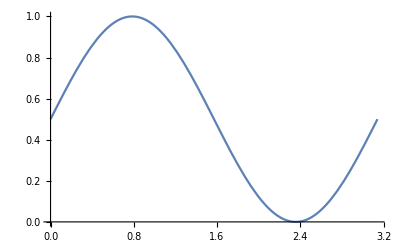

```mathematica
Plot[1/2+Cos[θ] Sin[θ],{θ,0,π}]
```